## MAP-Kinase in Solution

References
(1) Levchenko, A., Bruck, J., Sternberg, P.W. (2000). Scaffold proteins may biphasically affect the levels of mitogen-activated protein kinase signaling and reduce its threshold properties. Proc. Natl. Acad. Sci. USA97(11):5818–5823.
(2) Shapiro, B, Leevchenko A., Mjolsness E. (2001) Automatic Equation Generation for Signal Transduction with Applications to MAP-Kinase, in Foundations of Systems  Biology, Edited by H. Kitano, MIT Press.

```mathematica
<<xlr8r.m
```

xCellerator 0.89 (01-Sept-2012) loaded 01 September 2012 at 14:50 GMT-06:60 using Mathematica 8.0 for Linux x86 (64-bit) (October 10, 2011) (Version 8., Release 4) (MathSBML 1203-002)
GNU General Public License (GPL) Terms Apply.

## Canonical Form

```mathematica
{{Underoverscript[RAF⇄RAFp, RAFPH, RAFK]},{Underoverscript[MEK⇄MEKp⇄MEKpp, MEKPH, RAFp]},{Underoverscript[MAPK⇄MAPKp⇄MAPKpp, MAPKPH, MEKpp] }};
```

## Define the System

```mathematica
stn={
{Underoverscript[RAF⇄RAFp, RAFPH, RAFK], a1,d1,k1, a2,d2,k2},{Underoverscript[MEK⇄MEKp⇄MEKpp, MEKPH, RAFp], a3,d3,k3,a4,d4,k4,a5,d5,k5,a6,d6,k6 },
{Underoverscript[MAPK⇄MAPKp⇄MAPKpp, MAPKPH, MEKpp], a7,d7,k7,a8,d8,k8,a9,d9,k9,a10,d10,k10 }};
```

```mathematica
myrates={a1-> 1.,a2-> 0.5, a3-> 3.3,a4-> 10., a5-> 3.3,
a6-> 10., a7-> 20., a8-> 5., a9->20.,a10-> 5., d1->.4, d2->.5,  d3-> .42, d4-> .8, d5-> .4,
d6-> .8, d7-> .6, d8-> .4, d9-> .6, d10-> .4,k1-> .1,k2-> .1,k3-> .1,k4-> .1, k5-> .1,k6-> .1,k7-> .1,k8-> .1,k9-> .1,k10-> .1,
v1-> 0.1, K-> 0.3, k11-> .005};
```

```mathematica
myic={MEK->  0.2,MAPK-> 0.3,RAF-> 0.4,RAFPH-> .3,
MEKPH->  0.2 ,MAPKPH->0.3 ,RAFK-> 0.1};
```

## Translate reactions into differential equations

```mathematica
ODE[stn]//TableForm
```

MAPK'[t]==-a7 MAPK[t] MEKpp[t]+d7 Bind[MAPK,MEKpp][t]+k8 Bind[MAPKp,MAPKPH][t]
MAPKp'[t]==-a8 MAPKp[t] MAPKPH[t]-a9 MAPKp[t] MEKpp[t]+k7 Bind[MAPK,MEKpp][t]+d8 Bind[MAPKp,MAPKPH][t]+d9 Bind[MAPKp,MEKpp][t]+k10 Bind[MAPKPH,MAPKpp][t]
MAPKPH'[t]==-a8 MAPKp[t] MAPKPH[t]-a10 MAPKPH[t] MAPKpp[t]+d8 Bind[MAPKp,MAPKPH][t]+k8 Bind[MAPKp,MAPKPH][t]+d10 Bind[MAPKPH,MAPKpp][t]+k10 Bind[MAPKPH,MAPKpp][t]
MAPKpp'[t]==-a10 MAPKPH[t] MAPKpp[t]+k9 Bind[MAPKp,MEKpp][t]+d10 Bind[MAPKPH,MAPKpp][t]
MEK'[t]==-a3 MEK[t] RAFp[t]+d3 Bind[MEK,RAFp][t]+k4 Bind[MEKp,MEKPH][t]
MEKp'[t]==-a4 MEKp[t] MEKPH[t]-a5 MEKp[t] RAFp[t]+k3 Bind[MEK,RAFp][t]+d4 Bind[MEKp,MEKPH][t]+d5 Bind[MEKp,RAFp][t]+k6 Bind[MEKPH,MEKpp][t]
MEKPH'[t]==-a4 MEKp[t] MEKPH[t]-a6 MEKPH[t] MEKpp[t]+d4 Bind[MEKp,MEKPH][t]+k4 Bind[MEKp,MEKPH][t]+d6 Bind[MEKPH,MEKpp][t]+k6 Bind[MEKPH,MEKpp][t]
MEKpp'[t]==-a7 MAPK[t] MEKpp[t]-a9 MAPKp[t] MEKpp[t]-a6 MEKPH[t] MEKpp[t]+d7 Bind[MAPK,MEKpp][t]+k7 Bind[MAPK,MEKpp][t]+d9 Bind[MAPKp,MEKpp][t]+k9 Bind[MAPKp,MEKpp][t]+k5 Bind[MEKp,RAFp][t]+d6 Bind[MEKPH,MEKpp][t]
RAF'[t]==-a1 RAF[t] RAFK[t]+d1 Bind[RAF,RAFK][t]+k2 Bind[RAFp,RAFPH][t]
RAFK'[t]==-a1 RAF[t] RAFK[t]+d1 Bind[RAF,RAFK][t]+k1 Bind[RAF,RAFK][t]
RAFp'[t]==-a3 MEK[t] RAFp[t]-a5 MEKp[t] RAFp[t]-a2 RAFp[t] RAFPH[t]+d3 Bind[MEK,RAFp][t]+k3 Bind[MEK,RAFp][t]+d5 Bind[MEKp,RAFp][t]+k5 Bind[MEKp,RAFp][t]+k1 Bind[RAF,RAFK][t]+d2 Bind[RAFp,RAFPH][t]
RAFPH'[t]==-a2 RAFp[t] RAFPH[t]+d2 Bind[RAFp,RAFPH][t]+k2 Bind[RAFp,RAFPH][t]
Bind[MAPK,MEKpp]'[t]==a7 MAPK[t] MEKpp[t]-d7 Bind[MAPK,MEKpp][t]-k7 Bind[MAPK,MEKpp][t]
Bind[MAPKp,MAPKPH]'[t]==a8 MAPKp[t] MAPKPH[t]-d8 Bind[MAPKp,MAPKPH][t]-k8 Bind[MAPKp,MAPKPH][t]
Bind[MAPKp,MEKpp]'[t]==a9 MAPKp[t] MEKpp[t]-d9 Bind[MAPKp,MEKpp][t]-k9 Bind[MAPKp,MEKpp][t]
Bind[MAPKPH,MAPKpp]'[t]==a10 MAPKPH[t] MAPKpp[t]-d10 Bind[MAPKPH,MAPKpp][t]-k10 Bind[MAPKPH,MAPKpp][t]
Bind[MEK,RAFp]'[t]==a3 MEK[t] RAFp[t]-d3 Bind[MEK,RAFp][t]-k3 Bind[MEK,RAFp][t]
Bind[MEKp,MEKPH]'[t]==a4 MEKp[t] MEKPH[t]-d4 Bind[MEKp,MEKPH][t]-k4 Bind[MEKp,MEKPH][t]
Bind[MEKp,RAFp]'[t]==a5 MEKp[t] RAFp[t]-d5 Bind[MEKp,RAFp][t]-k5 Bind[MEKp,RAFp][t]
Bind[MEKPH,MEKpp]'[t]==a6 MEKPH[t] MEKpp[t]-d6 Bind[MEKPH,MEKpp][t]-k6 Bind[MEKPH,MEKpp][t]
Bind[RAF,RAFK]'[t]==a1 RAF[t] RAFK[t]-d1 Bind[RAF,RAFK][t]-k1 Bind[RAF,RAFK][t]
Bind[RAFp,RAFPH]'[t]==a2 RAFp[t] RAFPH[t]-d2 Bind[RAFp,RAFPH][t]-k2 Bind[RAFp,RAFPH][t]

## Predict a Time Course

```mathematica
sim=run[stn,"IC"->myic,"rates"->myrates,
timeSpan->100,MaxSteps->25000];
```

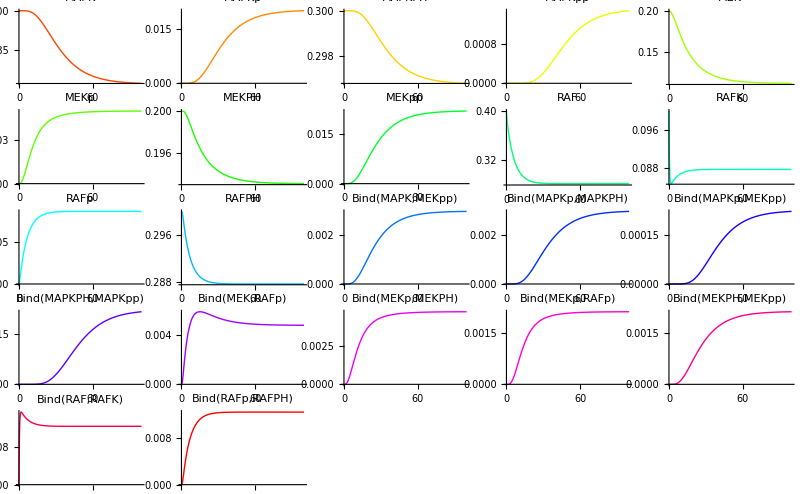

```mathematica
gridPlot[sim,plotColumns-> 5,ImageSize-> 800]
```